```mathematica
(*Tell Mathmetica to look inside the folder that contains this .nb file*)
SetDirectory[NotebookDirectory[]];
(*Get your csv file and insert the file path below. This brings Data into Mathematica*)
data=Import["myData.csv"]
(*This take the first row of the spreadsheet uses them as the "key" for each row*)
(*Notice that we are re-assigning this new format, a "Dataset" to the same name "data"*)
data=Dataset[Map[AssociationThread[First[data], #] &, Rest[data]]]
```

{{Date,Time,dateTime,dataDescription},{10/9/18,8:28,10/9/18 8:28:00,Sh},{10/9/18,8:41,10/9/18 8:41:00,Sh},{10/9/18,8:53,10/9/18 8:53:00,Sh},{10/9/18,8:53,10/9/18 8:53:00,Fu},{10/9/18,8:56,10/9/18 8:56:00,Fu},{10/9/18,8:56,10/9/18 8:56:00,Fu},{10/9/18,9:13,10/9/18 9:13:00,Pis off},{10/9/18,9:39,10/9/18 9:39:00,Fu},{10/9/18,9:39,10/9/18 9:39:00,Fu},{10/9/18,9:48,10/9/18 9:48:00,Gd dam},{10/9/18,9:58,10/9/18 9:58:00,Sh},{10/9/18,10:03,10/9/18 10:03:00,Sh},{10/9/18,10:16,10/9/18 10:16:00,Pis off},{10/9/18,10:40,10/9/18 10:40:00,Fu},{10/9/18,10:43,10/9/18 10:43:00,Sh},{10/9/18,10:47,10/9/18 10:47:00,Fu},{10/9/18,10:47,10/9/18 10:47:00,Fu},{10/9/18,10:56,10/9/18 10:56:00,Fu},{10/9/18,12:01,10/9/18 12:01:00,Bi},{10/9/18,12:05,10/9/18 12:05:00,Fu},{10/9/18,12:05,10/9/18 12:05:00,Fu},{10/9/18,12:06,10/9/18 12:06:00,Fu},{10/9/18,12:39,10/9/18 12:39:00,Fu},{10/9/18,1:06,10/9/18 1:06:00,As},{10/9/18,1:11,10/9/18 1:11:00,Fu},{10/9/18,1:11,10/9/18 1:11:00,Bi},{10/9/18,1:13,10/9/18 1:13:00,Fu},{10/9/18,1:14,10/9/18 1:14:00,Fu},{10/9/18,1:14,10/9/18 1:14:00,Fu},{10/9/18,1:14,10/9/18 1:14:00,Sh},{10/9/18,1:27,10/9/18 1:27:00,Fu},{10/9/18,1:28,10/9/18 1:28:00,Fu},{10/9/18,1:42,10/9/18 1:42:00,Gd dam},{10/9/18,1:44,10/9/18 1:44:00,Fu},{10/9/18,1:45,10/9/18 1:45,Fu},{10/9/18,1:45,10/9/18 1:45:00,Fu},{10/9/18,1:52,10/9/18 1:52:00,Sh},{10/10/18,9:16,10/10/18 9:16:00,Fu},{10/10/18,9:17,10/10/18 9:17:00,Fu},{10/10/18,9:58,10/10/18 9:58:00,Fu},{10/10/18,10:36,10/10/18 10:36:00,Fu},{10/10/18,10:38,10/10/18 10:38:00,Fu},{10/10/18,11:07,10/10/18 11:07:00,Sh},{10/10/18,11:10,10/10/18 11:10:00,Fu},{10/10/18,1:53,10/10/18 1:53:00,Sh},{10/10/18,1:56,10/10/18 1:56:00,Fu},{10/10/18,1:56,10/10/18 1:56:00,As},{10/10/18,1:56,10/10/18 1:56:00,Fu},{10/10/18,1:56,10/10/18 1:56:00,As},{10/10/18,1:56,10/10/18 1:56:00,Fu},{10/10/18,1:57,10/10/18 1:57:00,Bi},{10/10/18,1:57,10/10/18 1:57:00,Gd dam},{10/10/18,1:57,10/10/18 1:57:00,As},{10/10/18,2:09,10/10/18 2:09:00,Fu},{10/11/18,8:41,10/11/18 8:41:00,Fu},{10/11/18,8:42,10/11/18 8:42:00,Fu},{10/11/18,8:59,10/11/18 8:59:00,Fu},{10/11/18,9:15,10/11/18 9:15:00,Fu},{10/11/18,9:16,10/11/18 9:16:00,Fu},{10/11/18,9:16,10/11/18 9:16:00,Fu},{10/11/18,9:18,10/11/18 9:18:00,Fu},{10/11/18,9:26,10/11/18 9:26:00,Fu},{10/11/18,9:29,10/11/18 9:29:00,Fu},{10/11/18,9:36,10/11/18 9:36:00,Sh},{10/11/18,10:07,10/11/18 10:07:00,Fu},{10/11/18,11:02,10/11/18 11:02:00,As},{10/11/18,11:02,10/11/18 11:02:00,As},{10/11/18,11:12,10/11/18 11:12:00,Fu},{10/11/18,11:12,10/11/18 11:12:00,Sh},{10/11/18,12:07,10/11/18 12:07:00,Fu},{10/11/18,12:31,10/11/18 12:31:00,Fu}}

Dataset[<>]

```mathematica
(* Day 1:
F: 22 Sh: 8 Bi: 2 Pis: 2 Gd dam: 2 As: 1 *)
(* Day 2:
F: 10 Sh: 2 Bi: 1 Pis: 0 Gd dam: 1 As: 3 *)
(* Day 3:
F: 13 Sh: 2 Bi: 0 Pis: 0 Gd dam: 0 As: 2 *)
```

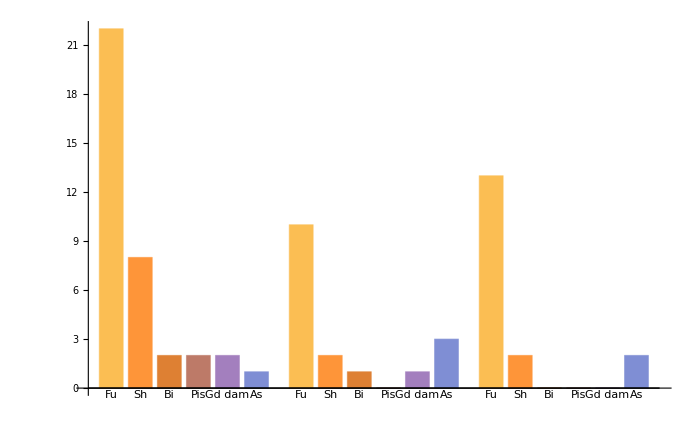

```mathematica
BarChart[{{22,8,2,2,2,1},{10,2,1,0,1,3},{13,2,0,0,0,2}},ChartLabels->{"Fu","Sh","Bi","Pis","Gd dam","As"}]
```

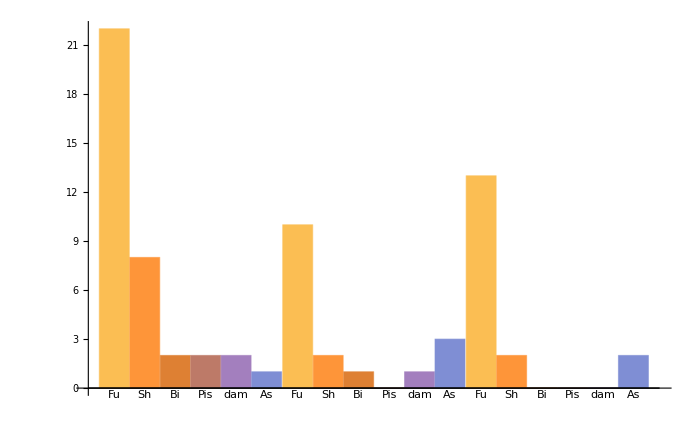

```mathematica
RectangleChart[{{{5,22},{5,8},{5,2},{5,2},{5,2},{5,1}},{{5,10},{5,2},{5,1},{5,0},{5,1},{5,3}},{{5,13},{5,2},{5,0},{5,0},{5,0},{5,2}}},ChartLabels->{ "Fu","Sh","Bi","Pis","dam","As"}]
```

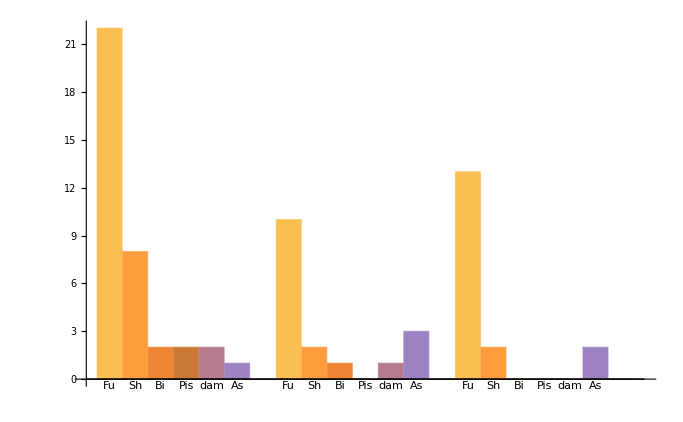

```mathematica
RectangleChart[{{{5,22},{5,8},{5,2},{5,2},{5,2},{5,1},{5,0}},{{5,10},{5,2},{5,1},{5,0},{5,1},{5,3},{5,0}},{{5,13},{5,2},{5,0},{5,0},{5,0},{5,2},{5,0}}},ChartLabels->{ "Fu","Sh","Bi","Pis","dam","As"," "}]
```

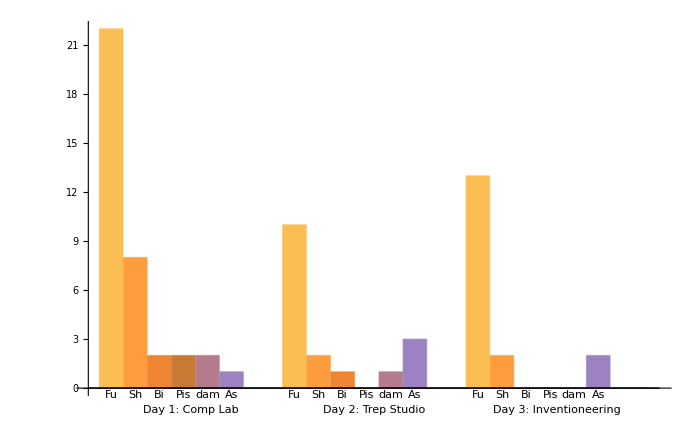

```mathematica
RectangleChart[{{{5,22},{5,8},{5,2},{5,2},{5,2},{5,1},{8,0}},{{5,10},{5,2},{5,1},{5,0},{5,1},{5,3},{8,0}},{{5,13},{5,2},{5,0},{5,0},{5,0},{5,2},{8,0}}},ChartLabels->{{"Day 1: Comp Lab","Day 2: Trep Studio","Day 3: Inventioneering"},{ "Fu","Sh","Bi","Pis","dam","As"," "}}]
```